## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PYK2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/home/mrama/Dropbox/MASSef/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PYK2_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(adp^c+pep^c→atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
pep | Null | 17602.3 | 16722.2
18482.4 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.00017 | 0.0001615
0.0001785 | pep | 0.005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.0005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00082 | 0.000779
0.000861 |  | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00019 | 0.0001805
0.0001995 | amp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00013 | 0.0001235
0.0001365 | g6p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.0007 | 0.000665
0.000735 | r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00082 | 0.000779
0.000861 | pi | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00036 | 0.000342
0.000378 | pep | 0.0005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 1.58 | 1.501
1.659 |  |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1.03 | 0.9785
1.0815 | amp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1 | 0.95
1.05 | g6p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 0.99 | 0.9405
1.0395 | r5p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 2.1 | 1.995
2.205 | pi | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | adp | 2 | 1.5
3 | pep | 0.0005 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = {0,0,0,0,0,0};
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0,0,0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(adp^c+pep^c→atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
pep | Null | 17602.3 | 16722.2
18482.4 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.00017 | 0.0001615
0.0001785 | pep | 0.005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.0005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[adp^c+pep^c->atp^c+pyr^c, PYK2]
```

(adp^c+pep^c→atp^c+pyr^c)^PYK2

```mathematica
catalyticBranch={"E_PYK2[c] + adp[c] <=> E_PYK2[c]&adp",
				"E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp",
				"E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp",
				"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c]",
				"E_PYK2[c]&atp <=> E_PYK2[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK21,((PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c)^PYK22,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK23,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c)^PYK24,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK21,Overscript[(PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c, PYK22],((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK23,Overscript[(PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c, PYK24],((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PYK2^c&pep^c&adp^c)_^-((PYK2^c&pyr^c&atp^c)_^)/K_PYK25) Volume_c k_PYK25^⟶}

Volume_c (-(PYK2^c&pyr^c&atp^c)_^ k_PYK25^⟵+(PYK2^c&pep^c&adp^c)_^ k_PYK25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.00023526054624980634;
FluxExpression = absoluteFlux /. {metabolite["pep", "c"] -> 0.00031351165489163315,metabolite["adp","c"]-> 0.0007078517944418567,
metabolite["pyr","c"]-> 0,metabolite["atp","c"]-> 0,
     parameter["PYK2_total"] -> 0.0000211170556057934, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "PYK2"] /. FluxExpression;
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	atp[c]	pep[c]	pyr[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17602.30756
1	0.000017000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909094
1	0.00002694318427183895	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.1368068886032101
1	0.000042702069335662915	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310194
1	0.0000676782189940945	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.00010726274856163285	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00017000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000001
1	0.0002694318427183895	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.0004270206933566291	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491988
1	0.0006767821899409458	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868985
1	0.0010726274856163284	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0017000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	0.000012000000000000007	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909095
1	0.00001901871830953338	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321014
1	0.000030142637178115006	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310197
1	0.00004777286046641966	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.0000757148813376232	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00012000000000000008	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000002
1	0.00019018718309533382	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.00030142637178115007	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491989
1	0.0004777286046641971	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	0.0007571488133762321	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0012000000000000008	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	0.000012000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909095
1	0.00001901871830953338	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321014
1	0.000030142637178115006	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310197
1	0.00004777286046641966	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.0000757148813376232	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00012000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000002
1	0.00019018718309533382	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.00030142637178115007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491989
1	0.0004777286046641971	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	0.0007571488133762321	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0012000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt"	0.00023526054624980634

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	adp[c]	atp[c]	pep[c]	pyr[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	17154.91366667523
1	0.000015645187989367234	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909091
1	0.000024795951939122515	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321008
1	0.00003929893542890824	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.2007600089131019
1	0.00006228461523224543	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.2847472489508012
1	0.00009871446267664559	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.38686317984685686
1	0.00015645187989367232	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5
1	0.00024795951939122514	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.00039298935428908234	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491987
1	0.0006228461523224549	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868984
1	0.000987144626766456	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.8631931113967899
1	0.0015645187989367234	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	0.00001360681157265288	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909095
1	0.000021565343032598655	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.1368068886032101
1	0.000034178765365454327	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310192
1	0.00005416969255443427	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.2847472489508018
1	0.0000858531769672342	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.0001360681157265288	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000001
1	0.00021565343032598655	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.0003417876536545433	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491989
1	0.0005416969255443422	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	0.000858531769672342	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.8631931113967901
1	0.001360681157265288	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909092
1	0.000011343261038322536	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909086
1	0.000017977857199946778	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321
1	0.00002849298349123367	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310178
1	0.000045158335568163064	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.2847472489508011
1	0.00007157113862485623	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.38686317984685664
1	0.00011343261038322536	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.4999999999999999
1	0.00017977857199946777	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.613136820153143
1	0.0002849298349123367	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491986
1	0.0004515833556816311	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868981
1	0.0007157113862485624	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.8631931113967899
1	0.0011343261038322535	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.184505592504767

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 1 of {} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 1 of {} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 1 of {} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	adp[c]	atp[c]	pep[c]	pyr[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0.000017000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909094
1	0.00002694318427183895	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.1368068886032101
1	0.000042702069335662915	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310194
1	0.0000676782189940945	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.00010726274856163285	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00017000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000001
1	0.0002694318427183895	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.0004270206933566291	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491988
1	0.0006767821899409458	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868985
1	0.0010726274856163284	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0017000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	0.000012000000000000007	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909095
1	0.00001901871830953338	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321014
1	0.000030142637178115006	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310197
1	0.00004777286046641966	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.0000757148813376232	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00012000000000000008	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000002
1	0.00019018718309533382	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.00030142637178115007	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491989
1	0.0004777286046641971	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	0.0007571488133762321	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0012000000000000008	0	0.0005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	0.000012000000000000007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909095
1	0.00001901871830953338	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321014
1	0.000030142637178115006	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310197
1	0.00004777286046641966	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.28474724895080133
1	0.0000757148813376232	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.386863179846857
1	0.00012000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000002
1	0.00019018718309533382	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	0.00030142637178115007	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491989
1	0.0004777286046641971	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	0.0007571488133762321	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	0.0012000000000000008	0	0.005	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909091
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateRev_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateRev_pyr.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateFor_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateRev_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/relRateRev_pyr.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PYK2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.06778308127
best_fit: 1.93139288013
best_fit: 3.01621177112
best_fit: 0.817182329821
best_fit: 1.072397952
best_fit: 1.09830378018
best_fit: 0.895132529741
best_fit: 0.402292121896
best_fit: 1.08573186298
best_fit: 0.892078682345

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | haldaneRatio_1 | 9.47814×10^-8 | 8.98352×10^-15 | 0.00384157 | 0.0000218242 | 17602.3 | 17602.3
1 | relRateFor_adp | 0.0726693 | 0.00528083 | 0.0165583 | 18.2141 | 0.0909091 | 0.107467
1 | relRateFor_adp | 0.0686975 | 0.00471934 | 0.0234458 | 17.1379 | 0.136807 | 0.160253
1 | relRateFor_adp | 0.0632231 | 0.00399715 | 0.0314603 | 15.6706 | 0.20076 | 0.23222
1 | relRateFor_adp | 0.056137 | 0.00315136 | 0.0392912 | 13.7986 | 0.284747 | 0.324038
1 | relRateFor_adp | 0.0476743 | 0.00227284 | 0.0448861 | 11.6026 | 0.386863 | 0.431749
1 | relRateFor_adp | 0.0384868 | 0.00148124 | 0.0463323 | 9.26645 | 0.5 | 0.546332
1 | relRateFor_adp | 0.0294898 | 0.000869646 | 0.0430797 | 7.02611 | 0.613137 | 0.656217
1 | relRateFor_adp | 0.0215261 | 0.000463373 | 0.0363453 | 5.08146 | 0.715253 | 0.751598
1 | relRateFor_adp | 0.0150839 | 0.000227525 | 0.0282469 | 3.53422 | 0.79924 | 0.827487
1 | relRateFor_adp | 0.0102418 | 0.000104894 | 0.0205982 | 2.38628 | 0.863193 | 0.883791
1 | relRateFor_adp | 0.00679963 | 0.000046235 | 0.0143454 | 1.57799 | 0.909091 | 0.923436
1 | relRateFor_adp | 0.0000199017 | 3.96078×10^-10 | 4.16585×10^-6 | 0.00458243 | 0.0909091 | 0.0909049
1 | relRateFor_adp | 0.0000162657 | 2.64573×10^-10 | 5.12376×10^-6 | 0.00374525 | 0.136807 | 0.136802
1 | relRateFor_adp | 0.0000111993 | 1.25425×10^-10 | 5.17701×10^-6 | 0.00257871 | 0.20076 | 0.200755
1 | relRateFor_adp | 4.54574×10^-6 | 2.06638×10^-11 | 2.98042×10^-6 | 0.00104669 | 0.284747 | 0.284744
1 | relRateFor_adp | 3.54416×10^-6 | 1.25611×10^-11 | 3.1571×10^-6 | 0.000816077 | 0.386863 | 0.386866
1 | relRateFor_adp | 0.0000125074 | 1.56434×10^-10 | 0.0000143998 | 0.00287997 | 0.5 | 0.500014
1 | relRateFor_adp | 0.0000214707 | 4.60992×10^-10 | 0.0000303131 | 0.00494394 | 0.613137 | 0.613167
1 | relRateFor_adp | 0.0000295611 | 8.73859×10^-10 | 0.0000486867 | 0.00680693 | 0.715253 | 0.715301
1 | relRateFor_adp | 0.0000362153 | 1.31155×10^-9 | 0.0000666505 | 0.00833923 | 0.79924 | 0.799307
1 | relRateFor_adp | 0.0000412823 | 1.70423×10^-9 | 0.0000820556 | 0.00950606 | 0.863193 | 0.863275
1 | relRateFor_adp | 0.0000449188 | 2.0177×10^-9 | 0.0000940316 | 0.0103435 | 0.909091 | 0.909185
1 | relRateFor_adp | 0.0646516 | 0.00417982 | 0.0125741 | 13.8315 | 0.0909091 | 0.078335
1 | relRateFor_adp | 0.0616055 | 0.00379523 | 0.0180927 | 13.225 | 0.136807 | 0.118714
1 | relRateFor_adp | 0.0573252 | 0.00328617 | 0.0248251 | 12.3656 | 0.20076 | 0.175935
1 | relRateFor_adp | 0.0516391 | 0.0026666 | 0.031922 | 11.2107 | 0.284747 | 0.252825
1 | relRateFor_adp | 0.044624 | 0.0019913 | 0.0377764 | 9.76479 | 0.386863 | 0.349087
1 | relRateFor_adp | 0.0367171 | 0.00134814 | 0.0405345 | 8.10689 | 0.5 | 0.459466
1 | relRateFor_adp | 0.0286635 | 0.000821596 | 0.0391606 | 6.38693 | 0.613137 | 0.573976
1 | relRateFor_adp | 0.021264 | 0.000452156 | 0.0341768 | 4.77828 | 0.715253 | 0.681076
1 | relRateFor_adp | 0.0150821 | 0.000227471 | 0.0272795 | 3.41318 | 0.79924 | 0.77196
1 | relRateFor_adp | 0.0103152 | 0.000106403 | 0.0202606 | 2.34717 | 0.863193 | 0.842932
1 | relRateFor_adp | 0.0068615 | 0.0000470801 | 0.01425 | 1.5675 | 0.909091 | 0.894841
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
1 | absRateFor | 1.14014×10^-6 | 1.29993×10^-12 | 0.0000788323 | 0.000262528 | 30.0281 | 30.0282
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261
3 | customRatio_1 | 1.08212×10^-8 | 1.17098×10^-16 | 5.86192×10^-12 | 2.49167×10^-6 | 0.000235261 | 0.000235261

### Simulated Data and Best Fit Data Plot

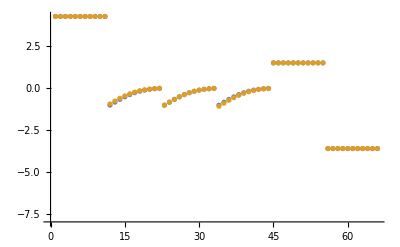

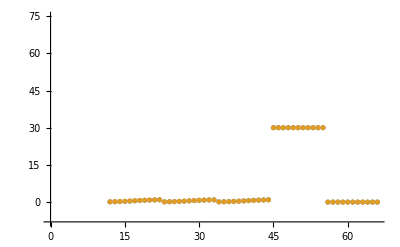

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

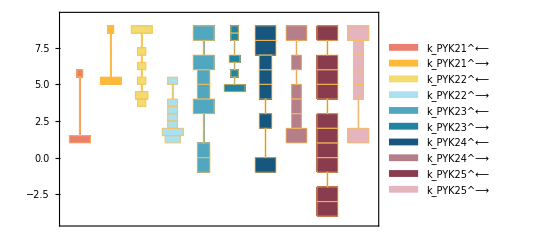

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

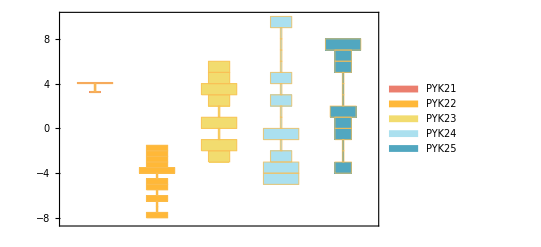

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

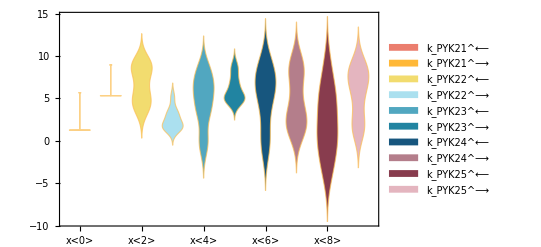

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

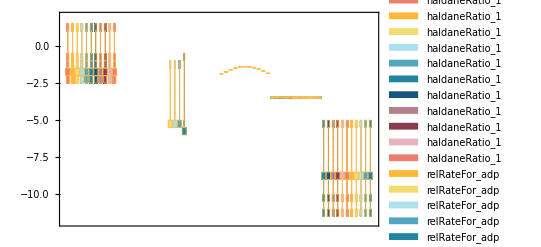

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

FindClusters::inerr: An internal error occured while evaluating FindClusters. Try different methods.

Part::partw: Part 2 of Log[Symbol[]] does not exist.

Part::partd: Part specification FindClusters[Log[Symbol[]]/Log[10],Method→{Optimize,Iterations→2}]⟦2,All,1⟧ is longer than depth of object.

Part::partd: Part specification FindClusters[Log[Symbol[]]/Log[10],Method→{Optimize,Iterations→2}]⟦2,All,2⟧ is longer than depth of object.

Part::partw: Part 2 of Log[Symbol[]] does not exist.

Part::partd: Part specification FindClusters[Log[Symbol[]]/Log[10],Method→{Optimize,Iterations→2}]⟦2,1,1⟧ is longer than depth of object.

Part::partd: Part specification FindClusters[Log[Symbol[]]/Log[10],Method→{Optimize,Iterations→2}]⟦2,1,2⟧ is longer than depth of object.

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

0.504033 | 6.84334 | 9. | 3.48477 | 3.72945 | 5.60742 | 8.98508 | 2.55274 | 8.71335 | 6.81329 | 3.3998 | 8.6853
0.302665 | 6.83612 | 9. | 2.49847 | 3.41773 | 5.57282 | 8.4452 | 8.21223 | 8.48635 | 9. | 8.72988 | 5.91734
0.403565 | 6.84537 | 8.93702 | 2.89026 | 3.79923 | 5.61764 | 8.93001 | 2.9612 | 4.37591 | 7.10803 | 2.61941 | 3.29776
0.596512 | 6.9085 | 8.99485 | 2.61851 | 5.40864 | 6.11723 | 8.99485 | 4.0603 | 2.01656 | 6.35182 | 7.98972 | 7.59992
0.530106 | 6.83522 | 8.99996 | 2.63507 | 3.36523 | 5.56857 | 9. | 3.06996 | 4.14564 | 5.88599 | 6.34476 | 8.04601

#### Parameter Cluster Plots (Optional)

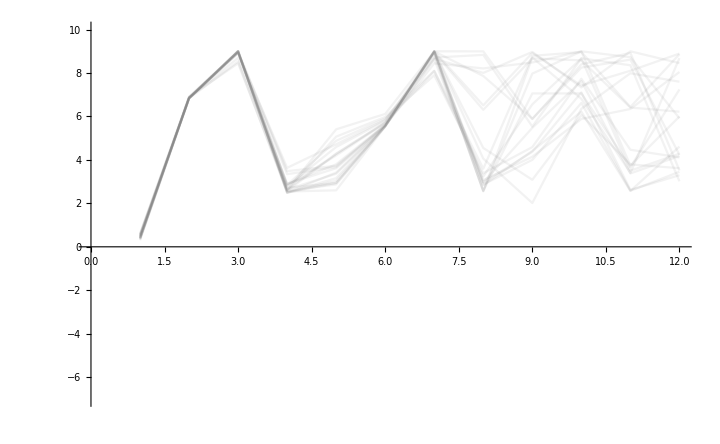

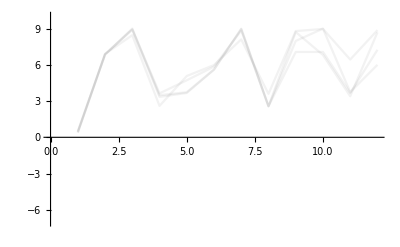
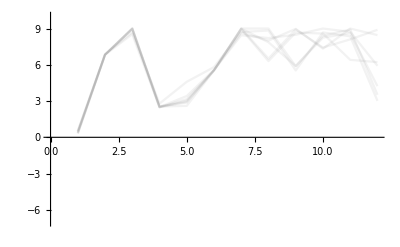
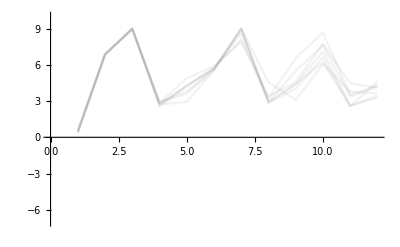
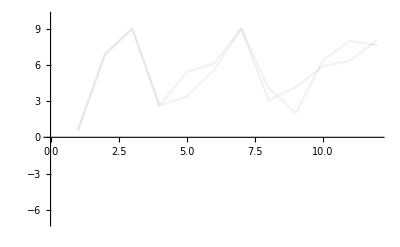

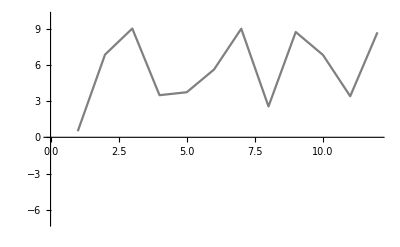
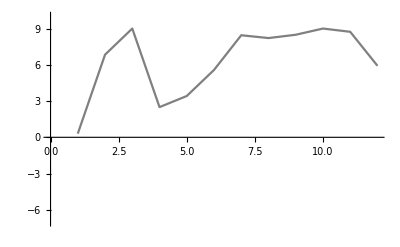
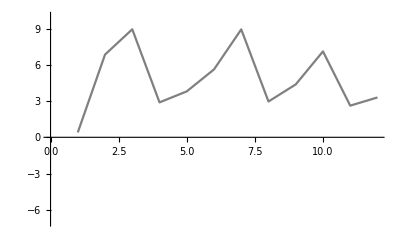

```mathematica
ListPlot[Log10[filteredDataListRed[[All,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.00017 | 0.00014117 | 16.9588
0.00012 | 0.000119993 | 0.00575907
0.00012 | 0.00014117 | 17.6417

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
30.0281 | 30.0282 | 0.000262528

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
17602.3 | 17602.3 | 0.0000218242

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
17602.3 | 17602.3 | 0.0000218242

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

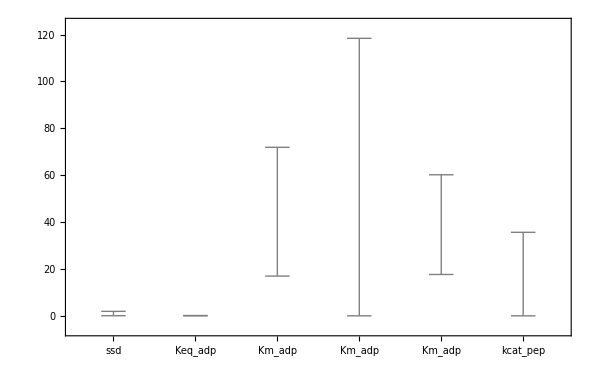

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pyk2 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\rateconst_labels_pyk2.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\S_pyk2.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PYK2[c],E_PYK2[c]&adp,E_PYK2[c]&atp,E_PYK2[c]&pep&adp,adp[c],atp[c],pep[c],pyr[c],E_PYK2[c]&pyr&atp}

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\species_pyk2.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PYK21: adp[c] + E_PYK2[c] <=> E_PYK2[c]&adp,PYK22: E_PYK2[c]&atp <=> atp[c] + E_PYK2[c],PYK23: E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp,PYK24: E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c],PYK25: E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp}

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\reactions_pyk2.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PYK2[c],E_PYK2[c]&adp,E_PYK2[c]&atp,E_PYK2[c]&pep&adp,E_PYK2[c]&pyr&atp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd*param_PYK2_total) - k_PYK21_rev*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd*param_PYK2_total - k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev*param_PYK2_total - k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*param_PYK2_total*pep(c) - k_PYK21_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*param_PYK2_total*pyr(c))/(adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd + k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK24_fwd + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd + k_PYK21_rev*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_fwd*k_PYK25_fwd + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev + k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK25_rev + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK25_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK25_rev*pep(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK24_rev*pyr(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_rev*k_PYK25_fwd*pyr(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + k_PYK21_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_rev*k_PYK25_fwd*pep(c)*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_rev*k_PYK25_fwd*pep(c)*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_rev*k_PYK25_rev*pep(c)*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_rev*k_PYK25_rev*pep(c)*pyr(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\rateconst_clusters_pyk2.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pyk2\rateLaw_pyk2.txt